# Introduction to 3D graphics

## Comprehension Questions

Math 250 - Mathematical Computing
Christopher Hanusa

### 10-1. Create a grid of spheres.

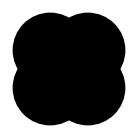

```mathematica
Graphics[{Disk[{0,0}],Disk[{1,0}],Disk[{0,1}],Disk[{1,1}]}]
```

```mathematica
Graphics[{Disk[{0,0},.2],Disk[{1,0},.2],Disk[{0,1},.2],Disk[{1,1},.2]}]
```

-Graphics-

```mathematica
Graphics[{
Disk[{0,0},.2],
Disk[{1,0},.2],
Disk[{0,1},.2],
Disk[{1,1},.2]
}]
```

```mathematica
Graphics[
Table[Disk[{x,y},.2],{x,0,1},{y,0,1}]
]
```

-Graphics-

```mathematica
Graphics3D[
Table[Ball[{x,y,z},.2],{x,0,1},{y,0,1},{z,0,1}]
]
```

-Graphics3D-

```mathematica
Graphics3D[
Table[Ball[{x,y,z},.2],{x,0,3,.4},{y,0,3},{z,0,3}]
]
```

-Graphics3D-

```mathematica
Graphics3D[{
Table[Ball[{x,y,z},.2],{x,0,3},{y,0,3},{z,0,3}],
Table[Text["Hello",{x,y,z}],{x,0,3},{y,0,3},{z,0,3}]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
Table[Ball[{x,y,z},.2],{x,0,3},{y,0,3},{z,0,3}],
Table[Text[Style[{x,y,z},Bold],{x,y,z}],{x,0,3},{y,0,3},{z,0,3}]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
Table[Ball[{x,y,z},.2],{x,0,3},{y,0,3},{z,0,3}],
Table[Text[Style[{x,y,z},Bold],{x,y,z}],{x,0,3},{y,0,3},{z,0,3}],
Red,Tube[{{0,0,0},{3,3,3}}]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
Table[Ball[{x,y,z},.2],{x,0,3},{y,0,3},{z,0,3}],
Table[Text[Style[{x,y,z},Bold],{x,y,z}],{x,0,3},{y,0,3},{z,0,3}],
Red,
Tube[{{0,0,0},{3,0,0}},.05],
Tube[{{0,0,1},{3,0,1}},.05],
Tube[{{0,0,2},{3,0,2}},.05],
Tube[{{0,0,3},{3,0,3}},.05],
Blue,
Tube[{{3,0,0},{3,3,0}},.05],
Tube[{{0,0,0},{0,3,0}},.05],
Tube[{{0,0,1},{0,3,1}},.05]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
Table[Ball[{x,y,z},.2],{x,0,3},{y,0,3},{z,0,3}],
(*Table[Text[Style[{x,y,z},Bold],{x,y,z}],{x,0,3},{y,0,3},{z,0,3}],*)
Red,
Table[Tube[{{0,j,k},{3,j,k}},.05],{j,0,3},{k,0,3}],
Blue,
Table[Tube[{{i,0,k},{i,3,k}},.05],{i,0,3},{k,0,3}],
Yellow,
Table[Tube[{{i,j,0},{i,j,3}},.05],{i,0,3},{j,0,3}],
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
Table[Cuboid[{x-.1,y-.1,z-.1},{x+.1,y+.1,z+.1}],{x,0,3},{y,0,3},{z,0,3}],
(*Table[Text[Style[{x,y,z},Bold],{x,y,z}],{x,0,3},{y,0,3},{z,0,3}],*)
Red,
Table[Tube[{{0,j,k},{3,j,k}},.05],{j,0,3},{k,0,3}],
Blue,
Table[Tube[{{i,0,k},{i,3,k}},.05],{i,0,3},{k,0,3}],
Yellow,
Table[Tube[{{i,j,0},{i,j,3}},.05],{i,0,3},{j,0,3}],
}]
```

-Graphics3D-

### 10-2. Create a square with some thickness. It should look something like this:

-Graphics3D-

### 10-3. Put spheres on the corners of your square from Question 2 using the Map command, similar to this:

### 10-4. Create three sides of a house using polygonal faces.

-Graphics3D-

#### Hint 1: (expand to see)

First determine the coordinates of each of the corners of the faces.

#### Hint 2: (expand to see)

You can create one face of the tetrahedron in this way:

```mathematica
v1={0,0,0};
v2={0,0,1};
v3={0,1,1};
v4={0,1,0};
```

```mathematica
Graphics3D[Polygon[{v1,v2,v3,v4}]]
```

### 10-5. Create a tetrahedron using PolyhedronData. Use one line of code.

### 10-6. Create an ice cream cone with three different flavors of ice cream, like this:

-Graphics3D-

Notes: Three Spheres, One Cone

Set up coordinate system!
For example, where are the centers of the spheres?

```mathematica
icecream=Graphics3D[{
White,Ball[{0,0,3.5}],
Brown,Ball[{0,0,4.5}],
Pink,Ball[{0,0,5.5}],
Lighter[Orange],Cone[{{0,0,3},{0,0,0.5}},.7]},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

```mathematica
BoundaryDiscretizeGraphics[icecream]
```

BoundaryDiscretizeGraphics::rnimpl: The function BoundaryDiscretizeGraphics is not implemented for .

BoundaryDiscretizeGraphics[-Graphics3D-]

```mathematica
Import[Export[NotebookDirectory[]<>"temp.stl",BoundaryDiscretizeGraphics[icecream]]]
```

-Graphics3D-

```mathematica
icecream=Graphics3D[{
Sphere[{0,0,3.5}],
Sphere[{0,0,4.5}],
Sphere[{0,0,5.5}],
Cone[{{0,0,3},{0,0,0.5}},.7]}]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"temp.stl",BoundaryDiscretizeGraphics[icecream]]]
```

BoundaryDiscretizeGraphics::brepl: There are components in  having dimension lower than the embedding dimension 3 that will not be included in the boundary representation.

-Graphics3D-

```mathematica
icecream=Show[{
DiscretizeGraphics[Sphere[{0,0,3.5}]],
DiscretizeGraphics[Sphere[{0,0,4.5}]],
DiscretizeGraphics[Sphere[{0,0,5.5}]],
BoundaryDiscretizeGraphics[Cone[{{0,0,3},{0,0,0.5}},.7]]}]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"temp.stl",icecream]]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Tube,MeshPrimitives[%,1]]]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Tube,MeshPrimitives[RegionUnion[
RegionUnion[{
BoundaryDiscretizeGraphics[Sphere[{0,0,3.5}],MaxCellMeasure->.0075],
BoundaryDiscretizeGraphics[Sphere[{0,0,4.5}],MaxCellMeasure->.0075]}],
BoundaryDiscretizeGraphics[Sphere[{0,0,2.5},1],MaxCellMeasure->.0075]],1]]]
```

-Graphics3D-